```mathematica
SetDirectory@FileNameJoin@{NotebookDirectory[],"..","talk"}
```

```mathematica
ringPoint[n_,r_:1]:=Sqrt[2]r Table[{Cos[2Pi/n i],Sin[2Pi/n i]},{i,0,n-1}];
```

```mathematica
ringSegments[n_,r_]:=Partition[ringPoint[n,r],2,1,{1,1}]
```

```mathematica
ring[n_,r_:1]:=Module[{points},
points=Sqrt[2]r Table[{Cos[2Pi/n i],Sin[2Pi/n i]},{i,0,n-1}];{Line[Table[points[[Mod[i,n,1]]],{i,1,n+1}]],
Line[Table[1.1points[[Mod[i,n,1]]],{i,1,n+1}]],
Table[Line[{points[[i]],1.1points[[i]]}],{i,1,n}],
Circle[{0,0},r]
}]
```

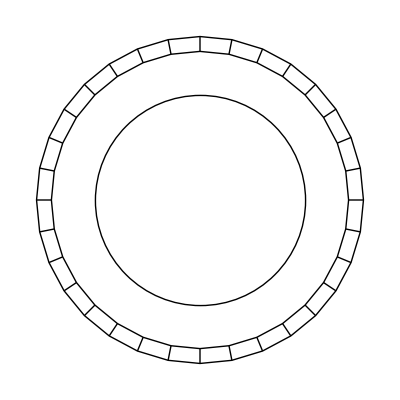

```mathematica
ring[32]//Graphics
```

```mathematica
Ellipse[p_,r_,theta_,t_]:={ColorData["DarkRainbow"][t],Rotate[Disk[p,r],theta,p]}
```

```mathematica
phantom={
Ellipse[{0,0},{.7,.9},0,0.1],
Ellipse[{-0.3,0.2},{0.25,0.5},-0.1,0.4],
Ellipse[{0.29,0.15},{0.25,0.5},0.1,0.5],
Ellipse[{-0.07,-0.5},{0.05,0.07},-0.1,0.88],
Ellipse[{0.035,-0.5},{0.05,0.07},0.2,0.99]
};
```

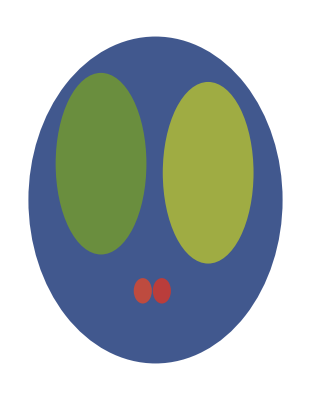

```mathematica
phantom//Graphics
```

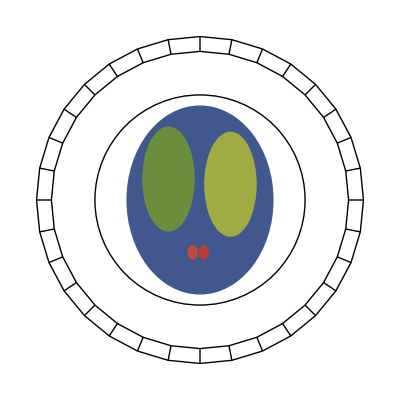

```mathematica
ringPhantom={ring[32],phantom}//Graphics
```

```mathematica
Export["ring_phantom.pdf",ringPhantom,"PDF"]
```

ring_phantom.pdf

```mathematica
intersect[line[p_,phi_],{p0_,p1_}]:=Module[{n={Sin[phi],-Cos[phi]},t},
t=n.(p1-p)/n.(p1-p0);
If[t≥0 && t≤1 , t p0+(1-t) p1,{}]
]
```

```mathematica
intersect[line[{0,0},Pi/2],{{0,1},{1,0}}]//N
```

{0.,1.}

```mathematica
trace[{p_,phi_},n_,r_:1]:={Line[Select[intersect[line[p,phi],#]& /@ringSegments[n,r],#≠{} &]],PointSize[0.015],Point[p]}
```

```mathematica
p1={0.035,-0.5}
p2={-0.2,0.5}
```

{0.035,-0.5}

{-0.2,0.5}

```mathematica
t1=trace[{p1,0.5},32,1]
t2=trace[{p2,-Pi/4},32,1]
```

{Line[{{1.39052,0.240526},{-0.95214,-1.03928}}],PointSize[0.015],Point[{0.035,-0.5}]}

{Line[{{-0.835226,1.13523},{1.13523,-0.835226}}],PointSize[0.015],Point[{-0.2,0.5}]}

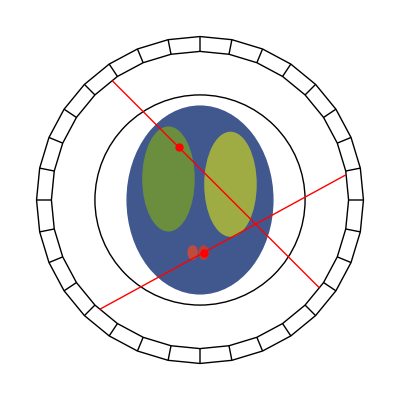

```mathematica
ringPhantomTrace={ring[32,1],phantom,Red,t1,t2}//Graphics
```

```mathematica
Export["ring_phantom_trace.pdf",ringPhantomTrace,"PDF"]
```

ring_phantom_trace.pdf

```mathematica
lorHit[{p_,phi_},n_,r_:1]:=(Position[intersect[line[p,phi],#]& /@ringSegments[n,r],{_,_}]//Flatten)-1
```

```mathematica
l1=lorHit[{p1,0.5},32,1]


l2=lorHit[{p2,-Pi/4},32,1]
```

{0,20}

{11,28}

```mathematica
Clear[lor]
```

```mathematica
lor[k_,l_,n_,r_:1]:=Module[{points},
points=Sqrt[2]Table[{Cos[2Pi/n i],Sin[2Pi/n i]},{i,0,n-1}];
{Opacity[0.1],EdgeForm[Black],Polygon[{points[[k+1]],points[[Mod[k+2,n,1] ]],points[[l+1]],points[[Mod[l+2,n,1]]]}]}]
```

```mathematica
lor[{k_,l_},n_,r_:1]:=lor[k,l,n,r]
```

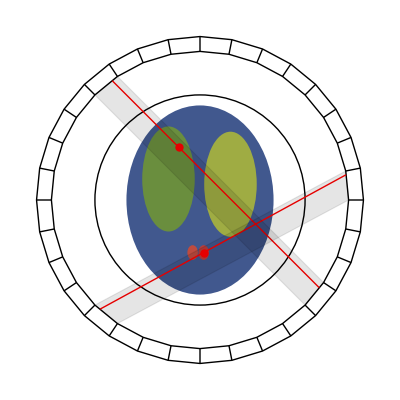

```mathematica
ringPhantomTraceLor={ring[32,1],phantom,Red,t1,t2,Black,lor[l1,32],lor[l2,32]}//Graphics
```

```mathematica
Export["ring_phantom_trace_lor.pdf",ringPhantomTraceLor,"PDF"]
```

ring_phantom_trace_lor.pdf

```mathematica
pixelGrid[n_,a_:1]:={Table[Line[{{-a,y},{a,y}}],{y,-a,a,2 a/n}],Table[Line[{{x,-a},{x,a}}],{x,-a,a,2 a/n}]
}
```

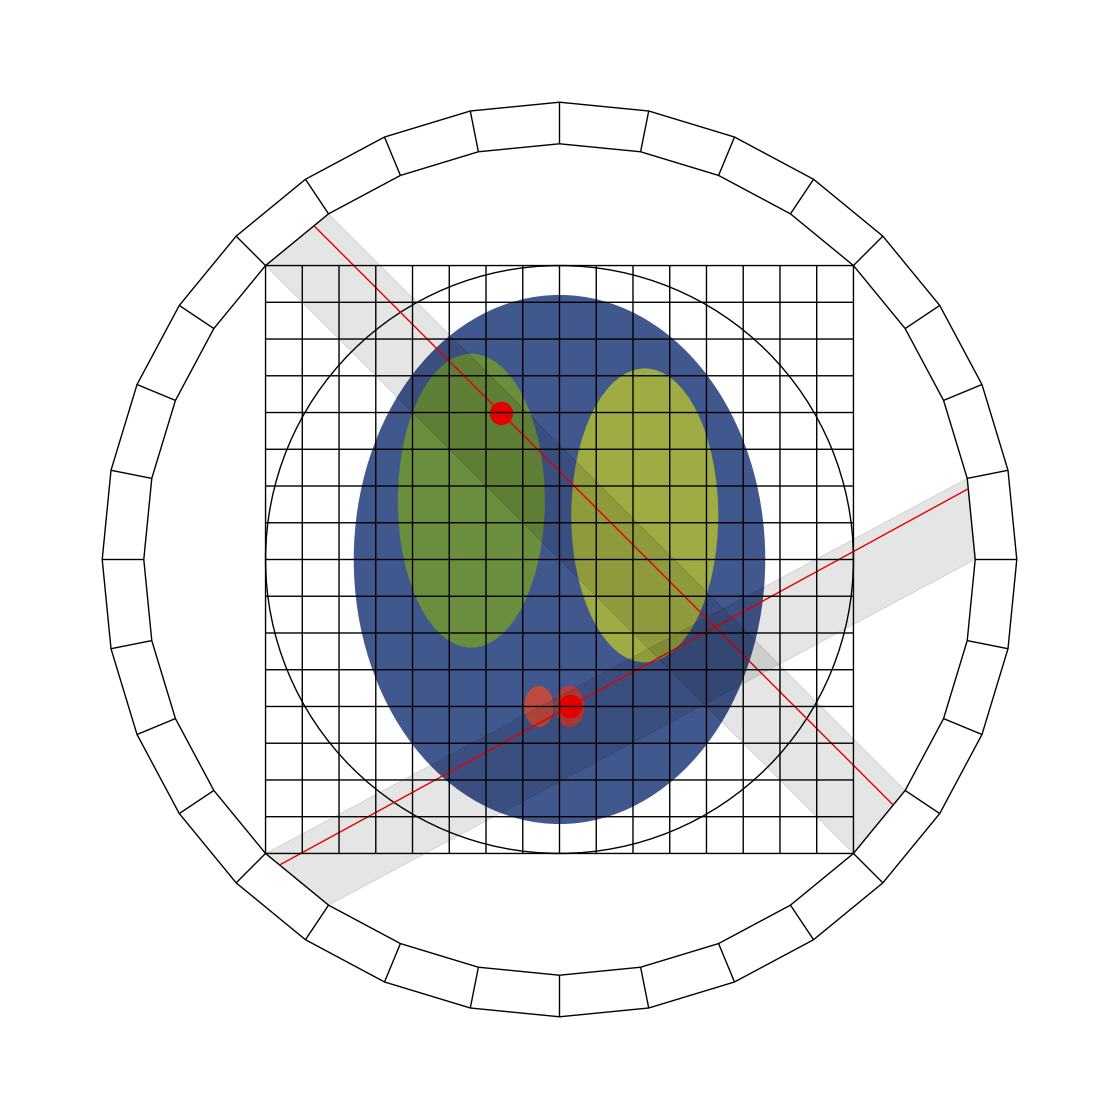

```mathematica
ringPhantomTraceLorGrid={ring[32,1],phantom,Red,t1,t2,Black,lor[l1,32],lor[l2,32],Black,pixelGrid[16,1]}//Graphics
```

```mathematica
Export["ring_phantom_trace_lor_grid.pdf",ringPhantomTraceLorGrid,"PDF"]
```

ring_phantom_trace_lor_grid.pdf

```mathematica
fan[i_,n_,r_:1]:=
Table[lor[i,Mod[i+n/4+k,n],n,r],{k,0,n/2}]
```

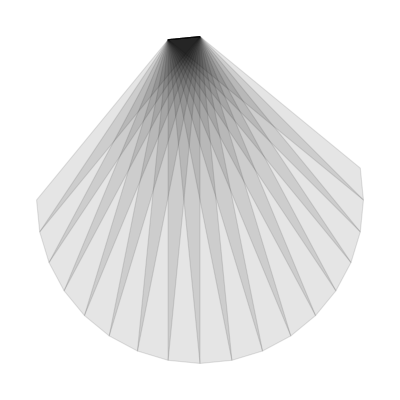

```mathematica
fan[8,32]//Graphics
```

```mathematica
p={x,y}+t{Cos[ϕ],Sin[ϕ]}
```

{x+t Cos[ϕ],y+t Sin[ϕ]}

```mathematica
Solve[p.p==R^2,t]
```

{{t→1/(2 (Cos[ϕ]^2+Sin[ϕ]^2))(-2 x Cos[ϕ]-2 y Sin[ϕ]-√((2 x Cos[ϕ]+2 y Sin[ϕ])^2-4 (-R^2+x^2+y^2) (Cos[ϕ]^2+Sin[ϕ]^2)))},{t→1/(2 (Cos[ϕ]^2+Sin[ϕ]^2))(-2 x Cos[ϕ]-2 y Sin[ϕ]+√((2 x Cos[ϕ]+2 y Sin[ϕ])^2-4 (-R^2+x^2+y^2) (Cos[ϕ]^2+Sin[ϕ]^2)))}}

```mathematica
%//Simplify
```

{{t→-x Cos[ϕ]-y Sin[ϕ]-√((R^2-y^2) Cos[ϕ]^2+(R^2-x^2) Sin[ϕ]^2+x y Sin[2 ϕ])},{t→-x Cos[ϕ]-y Sin[ϕ]+√((R^2-y^2) Cos[ϕ]^2+(R^2-x^2) Sin[ϕ]^2+x y Sin[2 ϕ])}}

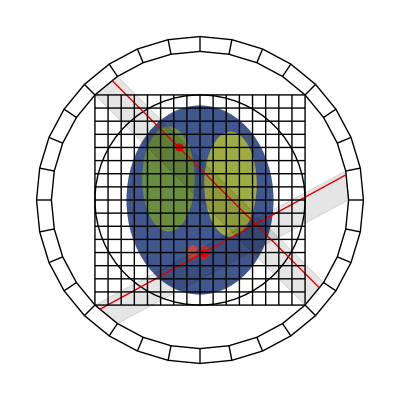

```mathematica
ringPhantomTraceLorGridCx={ring[32,1],phantom,Red,t1,t2,Black,lor[l1,32],lor[l2,32],Black,pixelGrid[16,1]}//Graphics
```

```mathematica
octant[n_,a_:1]:=Module[{size=2a/n},
{Opacity[0.25],Table[Rectangle[size{i,j},size{i+1,j+1}],{j,0,n/2-1},{i,j,n/2-1}]}]
```

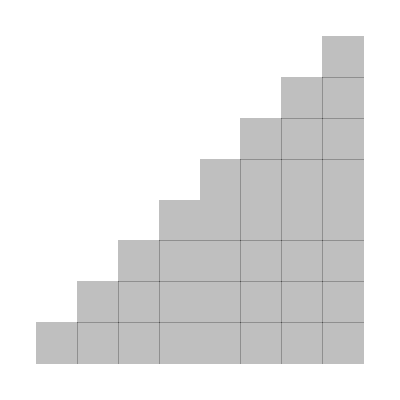

```mathematica
octant[16,1]//Graphics
```

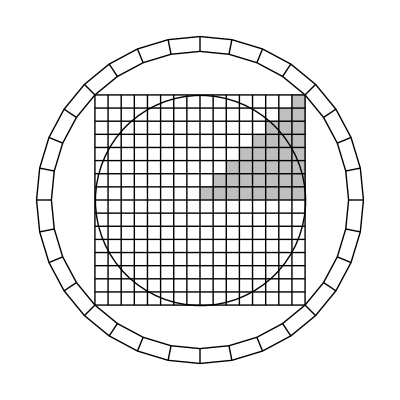

```mathematica
symetries={ring[32,1],pixelGrid[16,1],octant[16,1]}//Graphics
```

```mathematica
Export["symetries.pdf",symetries,"PDF"]
```

symetries.pdf